The biochemical resolving power of fluorescence lifetime imaging 

Andrew L. Trinh^(1,*) and Alessandro Esposito^1
^1 MRC Cancer Unit, University of Cambridge, Cambridge, United Kingdom
*at862@cam.ac.uk

Keywords: fluorescence lifetime, resolution, microscopy, biochemistry

Published in bioRxiv: doi_________

In this Notebook, we retrace the mathematical formalism presented in Kollner and Wolfrum (https://doi.org/10.1016/0009-2614(92)87068-Z)
We will generate Fig. 1 of their paper to provide an example of how to evaluate Fisher information and to test our analytical techniques used for the case of Gaussian IRFs in a different file. 

First, we initialize the Notebook and some parameters as defined in Kollner and Wolfrum.

```mathematica
(* Define subcripted symbols *)
<<Notation`
Symbolize[Subscript[σ, _]]

(* Define positivity of all variables, and set substitution rules *)
opts={B>0,α>0,m>1,i>1,τ>0,A>0,T>0,C>0,t≥0,p>0};
subs={τ->1/α,A->B α};
subsinv={α->1/τ,B->A/α};
```

We then make a convolution integral (f1) of a Dirac excitation pulse with an exponential decay starting from the origin. The number of photons emitted from t=0, to a generic time is the integral Λ[t].

```mathematica
f1=Convolve[DiracDelta[x],UnitStep[x] A Exp[-x/τ],x,y]
Λ[t_]=Integrate[f1//.subs,{y,0,t},Assumptions->opts]
```

A ⅇ^(-y/τ) UnitStep[y]

B-B ⅇ^(-t α)

The number of photons detected within a time bin is G[i]=Λ[i T]-Λ[(i-1)T], where i is the index bin and T is the bin width. With G[i] we indicate the expectation of Λ[i T]-Λ[(i-1)T], which is otherwise explicitly indicated with the analytical form of the integral Λ[t] to permit derivation of Λ[t] but not of the expectations.

```mathematica
LogL[B_,α_]=∑_(i=1)^m Log[Λ[i T]-Λ[(i-1)T]]G[i]-∑_(i=1)^m (Λ[i T]-Λ[(i-1)T])
```

-B+B ⅇ^(-m T α)+∑_(i=1)^m G[i] Log[B ⅇ^(-(-1+i) T α)-B ⅇ^(-i T α)]

The Fisher information matrix can be defined like

			I=(a | c
c | b)
			
where a, b, and c are:

```mathematica
a=Simplify[-D[LogL[B,α],{α,2}]//.{G[i]->(Λ[i T]-Λ[(i-1) T])},Assumptions->opts]
b=Simplify[-D[LogL[B,α],{B,2}]//.{G[i]->(Λ[i T]-Λ[(i-1) T])},Assumptions->opts]
c=Simplify[-D[LogL[B,α],{B,1},{α,1}]//.{G[i]->(Λ[i T]-Λ[(i-1) T])},Assumptions->opts]
```

-(B ⅇ^(-m T α) (-ⅇ^((1+m) T α)+m^2+ⅇ^(2 T α) m^2+ⅇ^(T α) (1-2 m^2)) T^2)/((-1+ⅇ^(T α))^2)

(1-ⅇ^(-m T α))/B

ⅇ^(-m T α) m T

Note that we have substituted G[i]→(Λ[i T]-Λ[(i-1) T]) only after differentiation as these now are the expectations. Next, the standard deviation on the parameter α can be evaluated from the top-left element of I^T, and σ_τ can be evaluated by error propagation from σ_α.

```mathematica
Subscript[σ, α]=√(b/(a b - c^2))//.subsinv
Subscript[σ, τ]=Simplify[√((D[τ/.subs[[1]],{α,1}])^2/.subsinv)Subscript[σ, α],Assumptions->opts]
```

√((1-ⅇ^(-(m T)/τ))/(A (-ⅇ^(-(2 m T)/τ) m^2 T^2-(ⅇ^(-(m T)/τ) (1-ⅇ^(-(m T)/τ)) (-ⅇ^(((1+m) T)/τ)+m^2+ⅇ^((2 T)/τ) m^2+ⅇ^(T/τ) (1-2 m^2)) T^2)/((-1+ⅇ^(T/τ))^2)) τ))

√((ⅇ^((m T)/τ) (-1+ⅇ^(T/τ))^2 (-1+ⅇ^((m T)/τ)) τ^3)/(A (ⅇ^(T/τ)+ⅇ^((T+2 m T)/τ)-ⅇ^((m T)/τ) m^2-ⅇ^(((2+m) T)/τ) m^2+2 ⅇ^(((1+m) T)/τ) (-1+m^2)) T^2))

We can now define the F^2-value. Note that with C we refer to the total number of photon counts actually measured. C is equal to the integral Λ[m T], fact that can be used to replace the amplitude A. 
FullSimplify can be used to return a compact equation as per Kollner and Wolfrum. However, we also define F2b. F2b is the very same quantity but its extended analytical form avoids undetermined operations of the type 0/0 or 1/0.

```mathematica
F2[τ_,m_,T_]=FullSimplify[C Subscript[σ, τ]^2/τ^2//.{Solve[(Λ[m T]//.subsinv)==C,A] [[1]][[1]]},Assumptions->opts]
F2b[p_,m_]=ExpandAll[C Subscript[σ, τ]^2/τ^2//.{Solve[(Λ[m T]//.subsinv)==C,A] [[1]][[1]]}//.{τ->m T p^-1}];
(* Expand All is used to avoid numerical issues with Mathematica *)
```

((-1+ⅇ^(T/τ))^2 (-1+ⅇ^((m T)/τ))^2 τ^2)/((ⅇ^(T/τ)+ⅇ^((T+2 m T)/τ)-ⅇ^((m T)/τ) m^2-ⅇ^(((2+m) T)/τ) m^2+2 ⅇ^(((1+m) T)/τ) (-1+m^2)) T^2)

Next we generate Fig. 1 from Kollner and Wolfrum.

```mathematica
mlist=2^Table[m,{m,1,10}];
LogLinearPlot[Evaluate@F2b[p,mlist],{p,1.,1000.},PlotRange->{0,10},PlotLabels->mlist]
```

-Graphics-

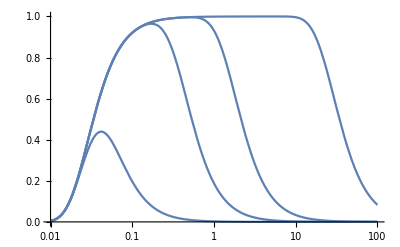

```mathematica
(* This is the photon-efficiency *)
LogLinearPlot[1/F2[τ,{2,16,64,1024},.1],{τ,0.01,100},PlotRange->{0,1}]
```